```mathematica
Solve[x==r*x*(1-x),x]
```

{{x→0},{x→(-1+r)/r}}

```mathematica
D[r*x*(1-x),x]
```

r (1-x)-r x

```mathematica
Simplify[r (1-x)-r x]
```

r-2 r x

```mathematica
Solve[r-2*r*(r-1)/r==0,r]
```

{{r→2}}

```mathematica
N[RecurrenceTable[{x[n+1]==2*x[n]*(1-x[n]),x[0]==1/2-1/100},x,{n,0,10}]]
```

{0.49,0.4998,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

```mathematica
rawsol=RecurrenceTable[{x[n+1]==2*x[n]*(1-x[n]),x[0]==1/2-1/100},x,{n,0,5}]
```

{49/100,2499/5000,6249999/12500000,39062499999999/78125000000000,1525878906249999999999999999/3051757812500000000000000000,2328306436538696289062499999999999999999999999999999999/4656612873077392578125000000000000000000000000000000000}

```mathematica
netsol=Table[{n-1,1/2-rawsol[[n]]},{n,6}]
```

{{0,1/100},{1,1/5000},{2,1/12500000},{3,1/78125000000000},{4,1/3051757812500000000000000000},{5,1/4656612873077392578125000000000000000000000000000000000}}

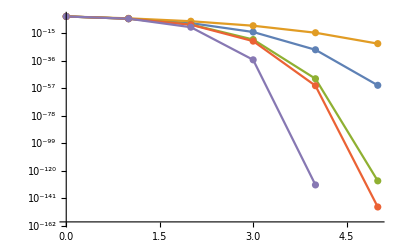

```mathematica
ListPlot[{netsol,fits,fits2,fits3,fits4},Joined->True,Mesh->All,PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
fits=Table[{n,3.6889*Exp[-5.9214*Exp[0.4412*n]]},{n,0,5}]
```

{{0,0.00989158},{1,0.000370776},{2,2.24933×10^-6},{3,8.04412×10^-10},{4,3.52802×10^-15},{5,1.65279×10^-23}}

```mathematica
nlm=NonlinearModelFit[netsol,a*Exp[-b*Exp[c*x]],{a,b,c},x,Method->"Newton",WorkingPrecision->50]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.83708589423614134727502674226464533951667897500793 ⅇ^(«1»)]

```mathematica
Normal[nlm]
```

0.83708589423614134727502674226464533951667897500793 ⅇ^(-4.4273416896719292223954080006137897323171809020403 ⅇ^(0.6331877661564583582260690649701742914738087307457 x))

```mathematica
fits2=Table[{n,0.114595*Exp[-2.43882*Exp[0.957073*n]]},{n,0,5}]
```

{{0,0.00999999},{1,0.0002},{2,7.5302×10^-9},{3,2.26908×10^-20},{4,2.26228×10^-50},{5,1.69535×10^-128}}

```mathematica
nlm2=NonlinearModelFit[netsol,a*Exp[-b*Exp[x]],{a,b},x,Method->"Newton"]
```

FittedModel[0.0974453 ⅇ^(-2.27671 ⅇ^x)]

```mathematica
Normal[nlm2]
```

0.0974453 ⅇ^(-2.27671 ⅇ^x)

```mathematica
fits3=Table[{n,0.0974453*Exp[-2.27671*Exp[n]]},{n,0,5}]
```

{{0,0.00999996},{1,0.000199998},{2,4.81658×10^-9},{3,1.34565×10^-21},{4,1.00961×10^-55},{5,1.75138×10^-148}}

```mathematica
fits4=Table[{n,0.0398*Exp[-1.3809*Exp[1.3437*n]]},{n,0,5}]
```

General::munfl: Exp[-1142.8] is too small to represent as a normalized machine number; precision may be lost.

{{0,0.0100038},{1,0.000200008},{2,6.13739×10^-11},{3,6.6391×10^-36},{4,1.32713×10^-131},{5,0.}}

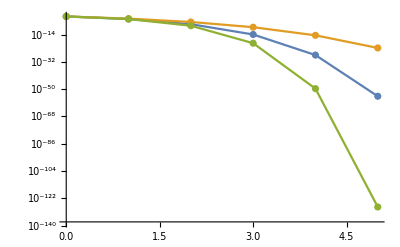

```mathematica
ListPlot[{netsol,fits,fits2},Joined->True,Mesh->All,PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
N[netsol[[1]]]
```

{0.,0.01}

```mathematica
fits5=Table[{n,(1/100)^(2^n)},{n,0,5}]
```

{{0,1/100},{1,1/10000},{2,1/100000000},{3,1/10000000000000000},{4,1/100000000000000000000000000000000},{5,1/10000000000000000000000000000000000000000000000000000000000000000}}

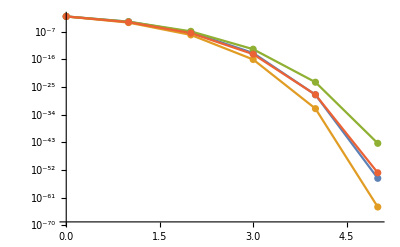

```mathematica
ListPlot[{netsol,fits5,fits6,fits7},Joined->True,Mesh->All,PlotRange->All,ScalingFunctions->"Log"]
```

```mathematica
nlm3=NonlinearModelFit[netsol,(1/100)^(a^x),{a},x,ConfidenceLevel->0.99]
```

FittedModel[100^(-1.84949^x)]

```mathematica
Normal[nlm3]
```

100^(-1.84949^x)

```mathematica
fits6=Table[{n,100^(-1.84949^n)},{n,0,5}]
```

{{0,0.01},{1,0.000199995},{2,1.44136×10^-7},{3,2.22444×10^-13},{4,3.97018×10^-24},{5,5.24485×10^-44}}

```mathematica
fits7=Table[{n,100^(-1.925^n)},{n,0,5}]
```

{{0,0.01},{1,0.000141254},{2,3.87927×10^-8},{3,5.41183×10^-15},{4,3.44102×10^-28},{5,1.35869×10^-53}}

```mathematica
N[netsol]
```

{{0.,0.01},{1.,0.0002},{2.,8.×10^-8},{3.,1.28×10^-14},{4.,3.2768×10^-28},{5.,2.14748×10^-55}}

```mathematica
N[fits5]
```

{{0.,0.01},{1.,0.0001},{2.,1.×10^-8},{3.,1.×10^-16},{4.,1.×10^-32},{5.,1.×10^-64}}

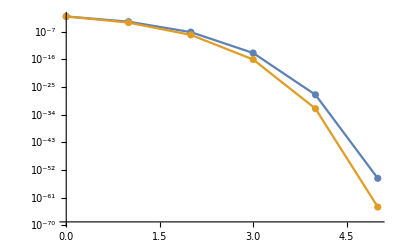

```mathematica
ListPlot[{netsol,fits5},Joined->True,Mesh->All,PlotRange->All,ScalingFunctions->"Log"]
```